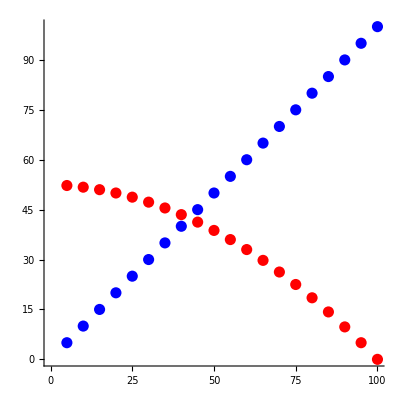

```mathematica
f[x_]=Sum[.05*(x+i),{i,5,100-x,5}];
Show[
Graphics[{PointSize[.02],Blue,Point[Table[{x,x},{x,5,100,5}]]}],
Graphics[{PointSize[.02],Red,Point[Table[{x,f[x]},{x,5,100,5}]]}],Axes->True,PlotRange->{{0,100},{0,100}}
,Axes->True,PlotRange->{{0,100},{0,100}}
]
```

```mathematica
f[x_]=Sum[.05*(x+i),{i,5,100-x,5}];
f[5]
```

52.25

```mathematica
f[10]
```

51.75

```mathematica
f[15]
```

51.

```mathematica
f[20]
```

50.

```mathematica
f[25]
```

48.75

```mathematica
f[100]
```

0.

```mathematica
f[95]
```

5.